# DrawPauliTransferMap

```mathematica
SetDirectory @ NotebookDirectory[];
Import["../Link/QuESTlink.m"];
```

## Doc

```mathematica
?DrawPauliTransferMap
```

## Correctness

## PTMap

PTMap_4[0→{{0,1}},1→{{1,Cos[x]},{2,Sin[x]}},2→{{1,-Sin[x]},{2,Cos[x]}},3→{{3,1}}]

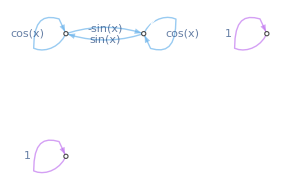

```mathematica
map = CalcPauliTransferMap @ Subscript[Rz, 4][x]
DrawPauliTransferMap[map]
```

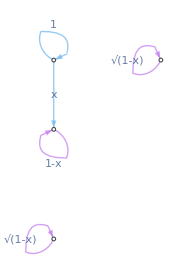

```mathematica
DrawPauliTransferMap @ CalcPauliTransferMap @ Subscript[Damp, 4][x]
```

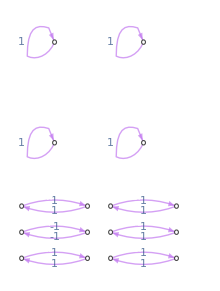

```mathematica
DrawPauliTransferMap @ CalcPauliTransferMap @ Subscript[C, 5][Subscript[X, 7]]
```

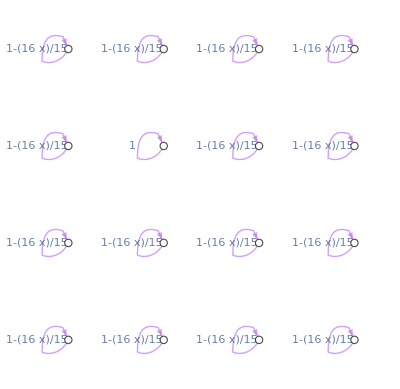

```mathematica
DrawPauliTransferMap @ CalcPauliTransferMap @ Subscript[Depol, 3,9][x]
```

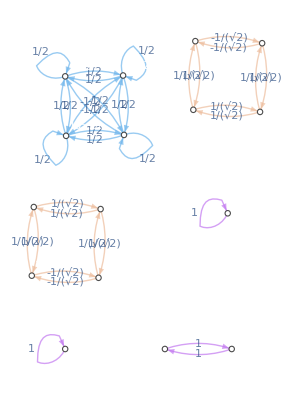

```mathematica
DrawPauliTransferMap @ CalcPauliTransferMap @ Subscript[C, 2][Subscript[H, 1]]
```

## PTM, gates, circuits

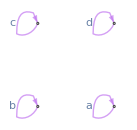

```mathematica
DrawPauliTransferMap @ Subscript[PTM, 0] @ DiagonalMatrix[{a,b,c,d}]
```

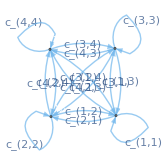

```mathematica
DrawPauliTransferMap @ Subscript[PTM, 0] @ Table[Subscript[c, i,j], {i,4},{j,4}]
```

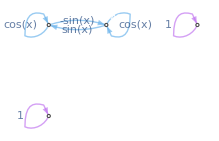

```mathematica
DrawPauliTransferMap @ Subscript[Rz, 0][x]
```

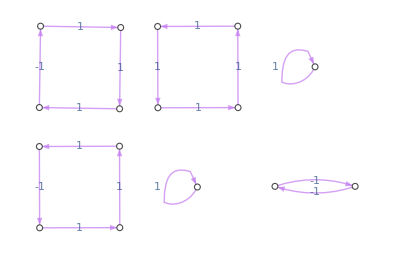

```mathematica
DrawPauliTransferMap @ Circuit[Subscript[H, 0] Subscript[C, 0][Subscript[X, 1]]]
```

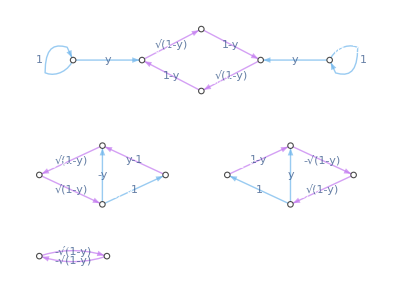

```mathematica
DrawPauliTransferMap @ Circuit[Subscript[H, 1] Subscript[Damp, 1][y]Subscript[C, 0][Subscript[X, 1]]]
```

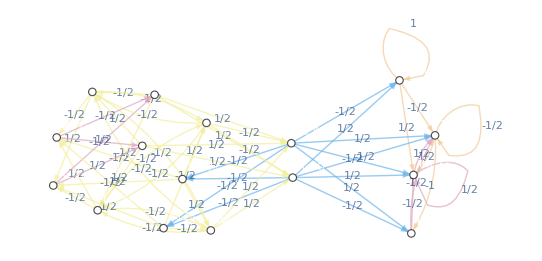

```mathematica
DrawPauliTransferMap[Subscript[U, 0,1] @ ({{0, 0, ⅈ, 0}, {0, 1, 0, 0}, {1, 0, 0, 1}, {0, 0, 0, 0}})]
```

## option “PauliStringForm”

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[C, 0][Subscript[X, 1]]];
```

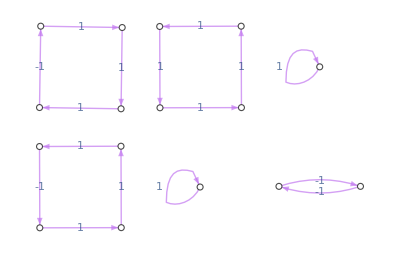

```mathematica
DrawPauliTransferMap[circ, "PauliStringForm" -> "String"]
```

```mathematica
DrawPauliTransferMap[circ, "PauliStringForm" -> "Kronecker"]
```

-Graphics-

```mathematica
DrawPauliTransferMap[circ, "PauliStringForm" -> "Index"]
```

-Graphics-

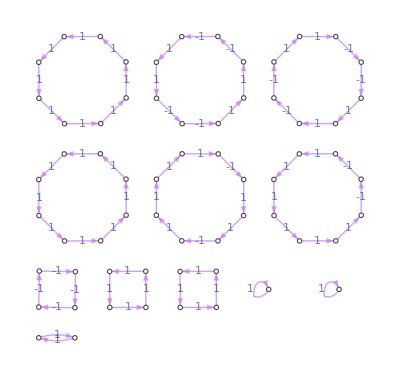

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[C, 0][Subscript[X, 1]] Subscript[SWAP, 1,2]];
DrawPauliTransferMap[circ, "PauliStringForm"->"Hidden"]
```

## option “ShowCoefficients”

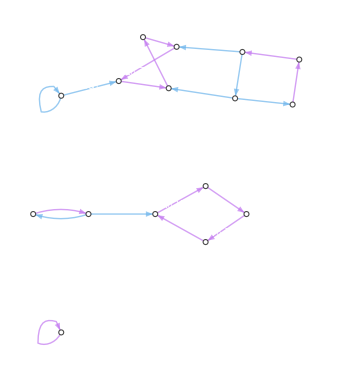

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[Depol, 0,1][x]Subscript[Damp, 1][y]Subscript[C, 0][Subscript[X, 1]]];
DrawPauliTransferMap[circ, "ShowCoefficients"->False]
```

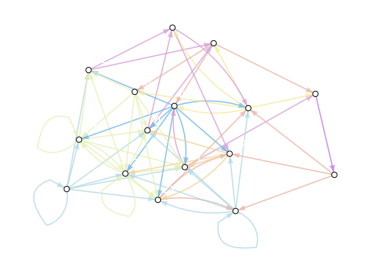

```mathematica
circ = Circuit[Subscript[H, 1] Subscript[Damp, 0][x] Subscript[Depol, 0,1][x] Subscript[C, 0][Subscript[X, 1]] Subscript[C, 1][Subscript[Rx, 0][x]] R[x,Subscript[X, 0] Subscript[Y, 1]]];
DrawPauliTransferMap[circ, 
	"ShowCoefficients"->False, 
	"PauliStringForm"->"String"]
```

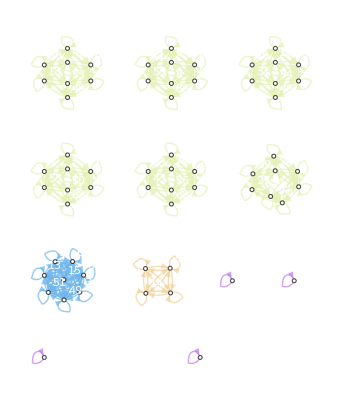

```mathematica
DrawPauliTransferMap[Subscript[C, 0,2][Subscript[H, 1]], 
	"ShowCoefficients"->False,
	"PauliStringForm"->"Index"]
```

```mathematica
DrawPauliTransferMap[Subscript[U, 0,1] @ ({{0, 0, a, 0}, {0, 1, 0, 0}, {1, 0, 0, 1}, {0, 0, 0, 0}}),
	"ShowCoefficients"->False, "PauliStringForm"->"Hidden"]
```

-Graphics-

## option “EdgeDegreeStyles”

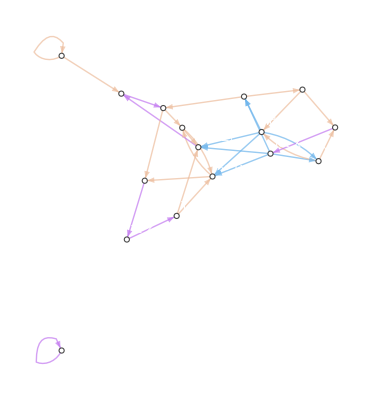

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[Depol, 0,1][x]Subscript[Rx, 0][a] Subscript[Damp, 1][y]Subscript[C, 0][Subscript[X, 1]]];
DrawPauliTransferMap[circ, "ShowCoefficients"->False]
```

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.7514516, 0.09778, 0.006329439999999999],RGBColor[0.9108294, 0.27453859999999997, 0.020955220000000004],RGBColor[0.9819778, 0.4844202000000001, 0.051441220000000024],RGBColor[1., 0.6815686000000001, 0.08952772000000002],RGBColor[1., 0.820127, 0.126955]}

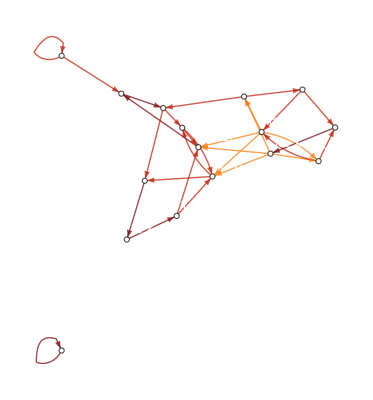

```mathematica
colors = ColorData["SolarColors"] /@ Range[0,1,.2]

DrawPauliTransferMap[circ, 
	"ShowCoefficients"->False,
	"EdgeDegreeStyles" ->colors]
```

## option AssertValidChannels

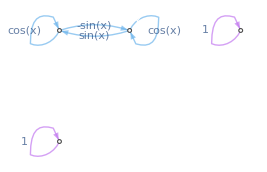

```mathematica
DrawPauliTransferMap[Subscript[Rx, 0][x], AssertValidChannels->True]
```

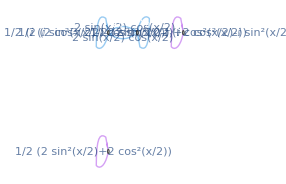

```mathematica
DrawPauliTransferMap[Subscript[Rx, 0][x], AssertValidChannels->False]
```

## options of Graph

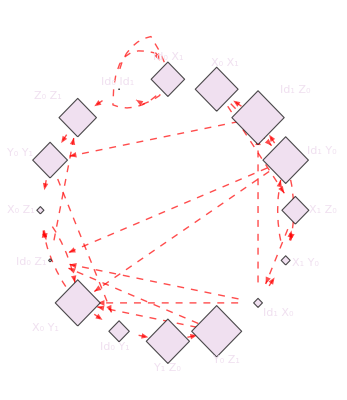

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[Depol, 0,1][x]Subscript[Rx, 0][a] Subscript[Damp, 1][y]Subscript[C, 0][Subscript[X, 1]]];
DrawPauliTransferMap[circ, "ShowCoefficients"->False,

	EdgeStyle->Directive[Red,Dashed],
	VertexShapeFunction -> "Diamond",
	VertexSize :> RandomReal[],
	VertexStyle ->LightPurple,
	GraphLayout -> "CircularEmbedding"
]
```

## Warnings

```mathematica
CalcPauliTransferMap[Subscript[Depol, 0][3/4]]
```

PTMap_0[0→{{0,1}},1→{},2→{},3→{}]

DrawPauliTransferMap::error: Warning: The Pauli transfer map produces no Pauli string from some initial strings. These edges (and null strings) are not being plotted. Hide this warning with Quiet[].

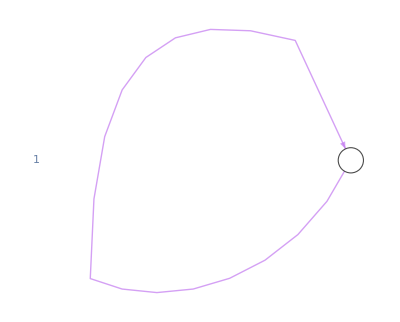

```mathematica
DrawPauliTransferMap[%]
```

## Errors

```mathematica
DrawPauliTransferMap[CalcPauliTransferMap[Subscript[X, 0]], "BadOption"->"bad"]
```

OptionValue::nodef: Unknown option BadOption for {DrawPauliTransferMap,Graph}.

$Failed

```mathematica
DrawPauliTransferMap[CalcPauliTransferMap[Subscript[X, 0]], "PauliStringForm"->"bad"]
```

DrawPauliTransferMap::error: Unrecognised value for option "PauliStringForm". See ?DrawPauliTransferMap

$Failed

```mathematica
DrawPauliTransferMap[ Subscript[PTMap, 0,-1][x] ]
```

DrawPauliTransferMap::error: Failed to automatically obtain the PTMap due to the below error:

CalcPauliTransferMatrix::error: Circuit contained an unrecognised or unsupported gate: PTMap_(0,1)[x]

$Failed

```mathematica
DrawPauliTransferMap[ ]
```

DrawPauliTransferMap::error: Invalid arguments. See ?DrawPauliTransferMap

$Failed

```mathematica
DrawPauliTransferMap @ Subscript[Bad, 0]
```

DrawPauliTransferMap::error: Failed to automatically obtain the PTMap due to the below error:

CalcPauliTransferMatrix::error: Circuit contained an unrecognised or unsupported gate: Bad_0

$Failed